# Simple neural network

#### theory

```mathematica
NeuralNetworkGraph[layers_List]:=Module[{graph,nodes,n},
graph=Flatten[Table[Table[{l,i}->{l+1,j},{i,layers[[l]]},{j,layers[[l+1]]}],{l,Length[layers]-1}]];
nodes=Union[graph[[All,1]]];
Graph[nodes,graph,GraphLayout->{"MultipartiteEmbedding","VertexPartition"->layers}]
]
```

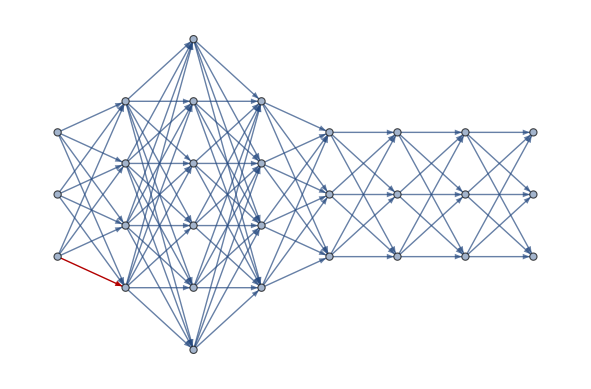

```mathematica
HighlightGraph[NeuralNetworkGraph[{3,4,6,4,3,3,3,3}],{{1,1}->{2,1}}]
```

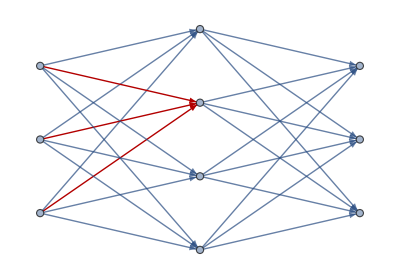

```mathematica
HighlightGraph[NeuralNetworkGraph[{3,4,3}],{{1,1}->{2,3},{1,2}->{2,3},{1,3}->{2,3}}]
```

#### implementation

```mathematica
FeedForward[x_,w_,b_]:=
Module[
{len,zz,aa,t},
len=Length[w];
zz=ConstantArray[Null,{len}];
aa=ConstantArray[Null,{len}];
Table[{zz[[i]],aa[[i]]}={t=(w[[i]].If[i===1,x,aa[[i-1]]]+b[[i]]),LogisticSigmoid[t]},{i,1,len}];
{zz,aa}
];
```

```mathematica
FeedBackward[a_,z_,x_,y_,w_]:=Module[{len,dσ,δ,gradw,gradb},
len=Length[w];
dσ[zz_]:=(1-LogisticSigmoid[zz]) LogisticSigmoid[zz];(*derivative of the σ function*)
δ=gradw=gradb=ConstantArray[Null,{len}];
δ[[len]]=(a[[len]]-y)*dσ[z[[len]]];(*initial backpropagation step*)
Do[δ[[i]]=(Transpose[w[[i+1]]].δ[[i+1]])*dσ[z[[i]]],{i,len-1,1,-1}];(*subsequent backpropagation steps*)
Do[gradw[[i]]=Outer[Times,δ[[i]],a[[i-1]]],{i,len,2,-1}];(*weight gradients, except final one*)
gradw[[1]]=Outer[Times,δ[[1]],x];(*final weight gradient*)
gradb=δ;(*bias gradient*)
{gradw,gradb}
];
```

```mathematica
NeuralNetwork[layers_List,data_]:=Module[{len,w,b,λ,dσ,y,z,a,δ,gradw,gradb,cost,tcost,cnt,tcnt,forward,x},
len=Length[layers];
w=Table[RandomReal[1,{layers[[i]],layers[[i-1]]}],{i,2,len}];(*init weights*)
b=Table[RandomReal[1,{layers[[i]]}],{i,2,len}];(*init biases*)
λ=0.05;(*learning rate*)
tcost=0;cost={};(*cost functions*)
cnt=Round[Length[data]/100];tcnt=0;(*cost iteration counters*)
Do[
{x,y}=d;
{z,a}=FeedForward[x,w,b];
tcost+=0.5*EuclideanDistance[y,a[[len-1]]]^2;(*cost function*)
If[Mod[++tcnt,cnt]===0,AppendTo[cost,tcost/cnt];tcost=0];
{gradw,gradb}=FeedBackward[a,z,x,y,w];
w=w-λ gradw;(*update weights*)
b=b-λ gradb;(*and biases*)
,
{d,data}];
<|"w"->w,"b"->b,"cost"->cost|>
];
```

train:

```mathematica
data=Table[{x=RandomInteger[{0,1},{3}],RotateLeft[x]},30000];
result=NeuralNetwork[{3,4,3},data];
```

test:

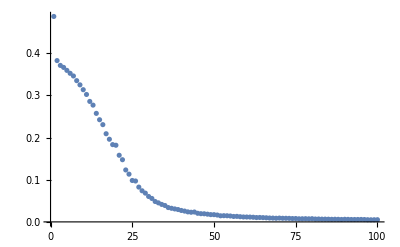

```mathematica
ListPlot[result["cost"],PlotRange->All]
```

```mathematica
ff=FeedForward[x=RandomInteger[{0,1},{3}],result["w"],result["b"]];
<|"x"->x,"actual"->RotateLeft[x],"prediction"->Round@ff[[-1,-1]]|>
```

<|x→{1,1,0},actual→{1,0,1},prediction→{1,0,1}|>

#### experiment

```mathematica
WeatherData["Chicago",{"Temperature","Pressure"}]
```

WeatherData::notent: "Chicago" is not a known entity, class, or tag for WeatherData. Use WeatherData[] for a list of entities.

WeatherData[Chicago,{Temperature,Pressure}]

```mathematica
WeatherData[Here,"Temperature",{DateObject[{2015,1,1}],DateObject[{2015,12,31}],"Day"}]
```

TimeSeries[…]

```mathematica
WeatherData[Here,"Pressure",{DateObject[{2015,1,1}],DateObject[{2015,12,31}],"Day"}]
```

TimeSeries[…]

```mathematica
WeatherData[Here,"SnowDepth",{DateObject[{2015,1,1}],DateObject[{2015,12,31}],"Day"}]
```

TimeSeries[…]

```mathematica
Normal[%]
```

{{Thu 1 Jan 2015 00:00:00GMT-6.,Missing[NotAvailable]},{Fri 2 Jan 2015 00:00:00GMT-6.,Missing[NotAvailable]},{Sat 3 Jan 2015 00:00:00GMT-6.,Missing[NotAvailable]},{Sun 4 Jan 2015 00:00:00GMT-6.,Missing[NotAvailable]},{Mon 5 Jan 2015 00:00:00GMT-6.,Missing[NotAvailable]},{Tue 6 Jan 2015 00:00:00GMT-6.,Missing[NotAvailable]},352,{Sat 26 Dec 2015 00:00:00GMT-6.,Missing[NotAvailable]},{Sun 27 Dec 2015 00:00:00GMT-6.,Missing[NotAvailable]},{Mon 28 Dec 2015 00:00:00GMT-6.,Missing[NotAvailable]},{Tue 29 Dec 2015 00:00:00GMT-6.,Missing[NotAvailable]},{Wed 30 Dec 2015 00:00:00GMT-6.,Missing[NotAvailable]},{Thu 31 Dec 2015 00:00:00GMT-6.,Missing[NotAvailable]}}
 |  |  |  |

```mathematica
%//Length
```

364